From https://reference.wolfram.com/language/guide/IntervalArithmetic.html :
The Wolfram Language automatically uses sophisticated algorithms to track the precision of approximate numbers. Particularly for some verification applications, however, it is convenient to maintain explicit numerical intervals. All the Wolfram Language’s basic mathematical functions and operations automatically operate on Interval objects.

Also, see 
https://reference.wolfram.com/language/tutorial/Numbers.html#9265
for more about Mathematica’s Interval operations.

In this notebook, we will verify a number of inequalities explicitly using Interval[], even when the inequality only involves single point evaluations of functions.  For example, we verify that the function

```mathematica
f[d_]=-440 Exp[-28 d/3]-130 Exp[-16 d/3]+96 Exp[-4 d]
```

-440 ⅇ^(-28 d/3)-130 ⅇ^(-16 d/3)+96 ⅇ^(-4 d)

is positive at d=1 by replacing d by a centered interval about 1 to compute an interval object.

```mathematica
interval=f[CenteredInterval[1,10^-2]]
```

Then the following logical statement alternatively verifies that the lower bound of the interval object is positive:

```mathematica
interval>0
```

True

or equivalently

```mathematica
Min[interval]>0
```

True

Note that, as in the above case,  none of the evaluations in this notebook require high precision.

```mathematica
Clear[f]
```

For the proof for 6 points when a>9.6, we shall verify several inequalities of the form h1[t] > h2[t] on an interval [a, b] for both increasing (actually this algorithm does not rely on h1 and h2 increasing) .  We use the following to check by subdividing the interval and establishing that the max of h2 is less than the min of h1 over the interval.

```mathematica
SegmentCheck[h1_,h2_,{a_,b_,n_}]:=Apply[And,Table[Min[h1[Interval[{a+k*(b-a)/n,a+(k+1)*(b-a)/n}]]]>Max[h2[Interval[{a+k*(b-a)/n,a+(k+1)*(b-a)/n}]]],{k,0,n-1}]]
```

We remark that the above module and be used for non-monotone functions involving elementary functions such as Sin, Cos, Exp, ArcCos, etc.  for which Mathematica has rigorous Interval computations.

# The small a case: a<Pi^2.

## Initializing truncated theta functions

```mathematica
Clear[d,x,k,j]
thetaest[x_,d_,j_]:=1+2Sum[Exp[-d k^2]Cos[2Pi k x],{k,j}];
thetaestt[t_,d_,j_]:=1+2Sum[Exp[-d k^2]Cos[k ArcCos[t]],{k,j}];
thetaestprime[x_,d_,j_]:=-2Sum[2Pi k Exp[-d k^2]Sin[2Pi k x],{k,j}];
thetaesttprime[t_,d_,j_]:=2Sum[ k Exp[-d k^2]Sin[k ArcCos[t]]/Sqrt[1-t^2],{k,j}];
thetaesttprime[1,d_,j_]:=2Sum[k^2Exp[-d k^2],{k,j}];
thetaesttprime[-1,d_,j_]:=2Sum[k^2Exp[-d k^2](-1)^(k+1),{k,j}];
thetaestprime2[x_,d_,j_]:=Sum[Exp[-k^2 d]2k(Cot[2Pi x]Sin[2Pi k x]-k Cos[2k Pi x])/(Sin[2Pi x]^2),{k,0,j}]
thetaesttprime2[1/2,d_,j_]:=thetaestprime2[1/6,d,j]
thetaesttprime2[-1/2,d_,j_]:=thetaestprime2[1/3,d,j]
interiorpoints={1/2,-1/2};
boundarypoints={1,-1};
points={1,1/2,-1/2,-1};
lowhigh={-1,1};
```

## Basic Value and Derivative Bounds

Here we encode the bounds from the small a portion of the appendix. f1 and f2 indicate whether we are a giving a bound on f1 or f2 as defined in the appendix. The first argument is 0,1, or 2 depending on whether we are considering value, first derivative, or second derivative, the second argument is the t value at which we are evaluating, and the third argument is -1 for a lower bound, 1 for an upper bound .

First the value bounds:

```mathematica
Clear[f1,f2]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[boundarypoints],j++,
f1[0,boundarypoints[[j]],lowhigh[[i]]]=thetaestt[boundarypoints[[j]],d,2]+lowhigh[[i]]*Exp[-4d]/50]]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[points],j++,
f2[0,points[[j]],lowhigh[[i]]]=thetaestt[points[[j]],d/3,4]+lowhigh[[i]]*Exp[-16d/3]/5]]
```

Now onto the first derivative bounds :

```mathematica
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[boundarypoints],j++,
f1[1,boundarypoints[[j]],lowhigh[[i]]]=thetaesttprime[boundarypoints[[j]],d,2]+lowhigh[[i]]*Exp[-4d]/8]]
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[points],j++,
f2[1,points[[j]],lowhigh[[i]]]=thetaesttprime[points[[j]],d/3,5]+4lowhigh[[i]]*Exp[-25d/3]]]
```

Finally the two second derivative bounds :

```mathematica
For [i=1,i<=Length[lowhigh],i++,For[j=1,j<= Length[interiorpoints],j++,
f2[2,interiorpoints[[j]],lowhigh[[i]]]=thetaesttprime2[interiorpoints[[j]],d/3,5]+lowhigh[[i]]*5Exp[-25d/3]]]
```

## 4 Points (Appendix Section C.2)

### 3rd order partial at (-1,1/2):

We need to show the third order mixed partial (1 derivative in t1, 2 in t2), evaluated at (-1, 1/2) is nonnegative for all d>=1. This result is lemma 16 and handled in appendix section C.2  The below quantity is a lower bound:

```mathematica
Clear[Val1,d]
t1=-1;
t2=1/2;
Val1[d_]=f1[1,t1,-1]f2[2,t2,-1]-f1[1,-t1,1]f2[2,-t2,1]//Expand
Clear[t1,t2]
```

-440 ⅇ^(-28 d/3)-130 ⅇ^(-16 d/3)+96 ⅇ^(-4 d)

By multiplying Val1[d] by Exp[4 d] (see below), we see it suffices to check positivity of Val1 at d = 1 because Val1[d]Exp[4d] increasing in d. See Lemma 40 for more detail on this kind of argument, which we use repeatedly in this notebook.

```mathematica
Exp[4d]Val1[d]//Expand
```

96-440 ⅇ^(-16 d/3)-130 ⅇ^(-4 d/3)

We use built-in Mathematica interval check to confirm that Val1 from (equation 93) in Appendix C.2 is positive:

```mathematica
Val1[CenteredInterval[1,10^-2]]
```

Then writing

```mathematica
Val1[CenteredInterval[1,10^-2]]>0
```

True

### Inequality string (Lemma 18):

We need to show A, B < C < D. (see Lemma 18, handled in appendix Section C.2)

#### D>C

Let C be 2 times partial of F with respect to t1 @ (-1, 1/2). Then C1, defined below, is an upper bound and C0 is a lower bound:

```mathematica
t1=-1;
t2=1/2;
b=1;
C1=2(f1[1,t1,b]f2[0,t2,b]-f1[1,-t1,-b]f2[0,-t2,-b])//Expand
b=-1;
C0=2(f1[1,t1,b]f2[0,t2,b]-f1[1,-t1,-b]f2[0,-t2,-b])//Expand
Clear[t1,t2,b]
```

63/2 ⅇ^(-28 d/3)+8/5 ⅇ^(-19 d/3)+63/2 ⅇ^(-16 d/3)-(95 ⅇ^(-4 d))/2+8 ⅇ^(-4 d/3)

65/2 ⅇ^(-28 d/3)-8/5 ⅇ^(-19 d/3)+65/2 ⅇ^(-16 d/3)-(97 ⅇ^(-4 d))/2+8 ⅇ^(-4 d/3)

Let D be the mixed partial of F w . r . t t1 @(-1, 1/2).  Then D0 is a lower bound:

```mathematica
t1=-1;
t2=1/2;
D0=f1[1,t1,-1]f2[1,t2,-1]+f1[1,-t1,-1]f2[1,-t2,-1]//Expand
Clear[t1,t2]
```

7/2 ⅇ^(-37 d/3)+72 ⅇ^(-28 d/3)-64 ⅇ^(-16 d/3)-1/2 ⅇ^(-13 d/3)+8 ⅇ^(-4 d/3)

Now the difference below is a lower bound for D-C, which we must show is positive for all d>=1:

```mathematica
D0-C1//Expand
```

7/2 ⅇ^(-37 d/3)+81/2 ⅇ^(-28 d/3)-8/5 ⅇ^(-19 d/3)-191/2 ⅇ^(-16 d/3)-1/2 ⅇ^(-13 d/3)+(95 ⅇ^(-4 d))/2

Dropping the two positive terms 7/2 ⅇ^(-37 d/3)+81/2 ⅇ^(-28 d/3), we may apply Lemma 40 and check the remainder is positive at d=1 to prove D0-C1>0 for all d>=1. We again use built-in Mathematica interval arithmetic to verify positivity and also provide a numerical confirmation.

```mathematica
Clear[Val2]
Val2[d_]=(D0-C1-7/2Exp[-37d/3]-81/2Exp[-28d/3])Exp[4d]//Expand
Val2[CenteredInterval[1,10^-2]]>0
```

95/2-8/5 ⅇ^(-7 d/3)-191/2 ⅇ^(-4 d/3)-ⅇ^(-d/3)/2

True

So C<D as desired.

#### A, B < C

Next, let A be 4 times the difference F (-1, 1) - F (-1, 1/2). Then A1 is an upper bound:

```mathematica
A1=4(f1[0,-1,1](f2[0,1,1]-f2[0,1/2,-1])+f1[0,1,-1](f2[0,-1,1]-f2[0,-1/2,-1]))//Expand
```

272/5 ⅇ^(-28 d/3)+(16 ⅇ^(-7 d))/25+376/5 ⅇ^(-16 d/3)+4/25 ⅇ^(-13 d/3)-64 ⅇ^(-4 d)+8 ⅇ^(-4 d/3)

Likewise let B be the partial of F with respect to t2 @ (-1, 1). Then B1 is an upper bound:

```mathematica
B1=f1[0,-1,1]f2[1,1,1]-f1[0,1,-1]f2[1,-1,-1]//Expand
```

18 ⅇ^(-37 d/3)-72 ⅇ^(-28 d/3)+8 ⅇ^(-25 d/3)+(18 ⅇ^(-7 d))/25+96 ⅇ^(-16 d/3)+2/25 ⅇ^(-13 d/3)-72 ⅇ^(-4 d)+8 ⅇ^(-4 d/3)

By Lemma 40, the positivity of Val3 (below) for all d >= 1 follows from checking positivity when d = 1.

```mathematica
Val3[d_]=(C0-A1)//Expand
Val3[CenteredInterval[1,10^-2]]>0
```

-219/10 ⅇ^(-28 d/3)-(16 ⅇ^(-7 d))/25-8/5 ⅇ^(-19 d/3)-427/10 ⅇ^(-16 d/3)-4/25 ⅇ^(-13 d/3)+(31 ⅇ^(-4 d))/2

True

Therefore C > A as desired .

The same logic shows Val4 is positive for all d >= 1.

```mathematica
(C0 - B1) // Expand
Val4[d_] = Exp[4 d] (C0 - B1 - 209/2 Exp[-28 d/3]) // Expand
Val4[CenteredInterval[1, 10^-2]] > 0
```

-18 ⅇ^(-37 d/3)+209/2 ⅇ^(-28 d/3)-8 ⅇ^(-25 d/3)-(18 ⅇ^(-7 d))/25-8/5 ⅇ^(-19 d/3)-127/2 ⅇ^(-16 d/3)-2/25 ⅇ^(-13 d/3)+(47 ⅇ^(-4 d))/2

47/2-18 ⅇ^(-25 d/3)-8 ⅇ^(-13 d/3)-(18 ⅇ^(-3 d))/25-8/5 ⅇ^(-7 d/3)-127/2 ⅇ^(-4 d/3)-(2 ⅇ^(-d/3))/25

True

Therefore C > B as desired, which completes appendix Section C.2.

## 6 Points (Appendix Section C.3)

### Coefficient bounds

Before we can prove the necessary derivative conditions are satisfied (equations 97-99), we must compute upper and lower bounds for the coefficients b10 and b02.

First, recall b10 = 1/2(f1 (1) f2 (-1/2) - f1 (-1) f2 (1/2) + f1 (-1) f2' (1/2)). We’ll use b10l and b10h to denote lower and upper bounds, respectively.

```mathematica
p=-1;
b10l=1/2(f1[0,1,p]f2[0,-1/2,p]-f1[0,-1,-p]f2[0,1/2,-p]+f1[0,-1,p]f2[1,1/2,p])//Expand;
p=1;
b10h=1/2(f1[0,1,p]f2[0,-1/2,p]-f1[0,-1,-p]f2[0,1/2,-p]+f1[0,-1,p]f2[1,1/2,p])//Expand;
Clear[p]
```

We’ll do the same for b02 = 4/9 f1 (-1) (f2 (-1) - f2 (1/2) + 3/2 f2' (1/2))

```mathematica
p=-1;
b02l=4/9f1[0,-1,p](f2[0,-1,p]-f2[0,1/2 ,-p]+3/2f2[1,1/2,p])//Expand;
p=1;
b02h=4/9f1[0,-1,p](f2[0,-1,p]-f2[0,1/2 ,-p]+3/2f2[1,1/2,p])//Expand;
```

### Necessary Derivative conditions (equations 97-99)

#### (-1, -1)

Now we can check the derivative condition at (-1,-1), that is f1’(-1)f2(-1)-b10+b02 >0. The below is a lower bound

```mathematica
f1[1,-1,-1]f2[0,-1,-1]-b10h+b02l//Expand
```

-621/50 ⅇ^(-37 d/3)-(7591 ⅇ^(-28 d/3))/3000-19/3 ⅇ^(-25 d/3)+(49 ⅇ^(-7 d))/4+268/45 ⅇ^(-19 d/3)-2291/180 ⅇ^(-16 d/3)+1623/100 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200-2 ⅇ^(-3 d)+2 ⅇ^(-7 d/3)

We break this large sum into Val1[d]+Val2[d]+Val3[d], as defined below, and show each is positive for all d>=1.

```mathematica
Val1[d_]=-621/50 ⅇ^(-37 d/3)-(7591 ⅇ^(-28 d/3))/3000-19/3 ⅇ^(-25 d/3)+(49 ⅇ^(-7 d))/4+268/45 ⅇ^(-19 d/3);
Val2[d_]=-2291/180 ⅇ^(-16 d/3)+5Exp[-13d/3];
Val3[d_]=1123/100 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200-2 ⅇ^(-3 d)+2 ⅇ^(-7 d/3);
```

The positivity of Val1[d] and Val2[d] each follow immediately by applying Lemma 40 and checking Val1[1] > 0, Val2[1] > 0, which are handled below :

```mathematica
Val1[CenteredInterval[1,1/10]]>0
Val2[CenteredInterval[1,1/1000]]>0
```

True

True

It remains to show Val3[d] is positive for all d >= 1, or equivalently that Exp[3d]Val3[d]>0 for all d>=1. We first check Val3[1]>0, which certainly implies Val3[1]Exp[3]>0.

```mathematica
Val3[CenteredInterval[1,1/1000]]>0
```

True

Now we claim Val3[d] Exp[3 d] is increasing for d >= 1 which would complete the proof. Call this derivative Val4[d].

```mathematica
D[Exp[3d]Val3[d],d]//Expand
Val4[d_]=-1123/75 ⅇ^(-4 d/3)+(2429 ⅇ^-d)/200+4/3 ⅇ^(2 d/3)
```

-1123/75 ⅇ^(-4 d/3)+(2429 ⅇ^-d)/200+4/3 ⅇ^(2 d/3)

-1123/75 ⅇ^(-4 d/3)+(2429 ⅇ^-d)/200+4/3 ⅇ^(2 d/3)

To show Val4[d] > 0 for all d >= 1, we can apply Lemma 40 and check Val4[1] > 0, as below :

```mathematica
Val4[CenteredInterval[1,1/100]]>0
```

True

#### (1, -1/2)

the necessary derivative condition at (-1, 1/2) is b10-b02/2-f1' (1) f2 (-1/2) > 0. Below is a lower bound:

-(f1[1, 1, 1] f2[0, -1/2, 1] - b10l + b02h/2) // Expand

-491/50 ⅇ^(-37 d/3)+(13568 ⅇ^(-28 d/3))/1125-5 ⅇ^(-25 d/3)-(49 ⅇ^(-7 d))/4+34/9 ⅇ^(-19 d/3)+(10397 ⅇ^(-16 d/3))/1800+1621/200 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200+2 ⅇ^(-3 d)

We decompose this upper bound into Val5 + Val6 + Val7 and show each part is positive for all d>=1 :

```mathematica
Val5[d_]=-491/50 ⅇ^(-37 d/3)-5 ⅇ^(-25 d/3)-(49 ⅇ^(-7 d))/4+34/9 ⅇ^(-19 d/3)+(3000 ⅇ^(-16 d/3))/1800;
Val6[d_]=(13568 ⅇ^(-28 d/3))/1125;
Val7[d_]=(7397 ⅇ^(-16 d/3))/1800+1621/200 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200+2 ⅇ^(-3 d);
```

Val 6 is clearly positive. By Lemma 40, it follows Val5[d]>0 for all d>=1 if Val5[1]>0, which we check below:

```mathematica
Val5[CenteredInterval[1,1/100]]>0
```

True

So it remains to show Val7[d]>0 for all d>=1. As in the (-1,-1) section, we equivalently show Val7[d]Exp[3d]>0 by showing it is positive at d=1 and increasing for all d>=1. First we verify the inequality at d=1:

```mathematica
Val7[CenteredInterval[1,1/1000]]>0
```

True

Now taking the derivative, which we call Val8[d]:

```mathematica
D[Val7[d]Exp[3d],d]//Expand
Val8[d_]=-(51779 ⅇ^(-7 d/3))/5400-1621/150 ⅇ^(-4 d/3)+(2429 ⅇ^-d)/200
```

-(51779 ⅇ^(-7 d/3))/5400-1621/150 ⅇ^(-4 d/3)+(2429 ⅇ^-d)/200

-(51779 ⅇ^(-7 d/3))/5400-1621/150 ⅇ^(-4 d/3)+(2429 ⅇ^-d)/200

We see that showing Val8[d] > 0 for all d >= 1 follows from Lemma 40 and checking Val8[1] > 0

```mathematica
Val8[CenteredInterval[1,1/1000]]>0
```

True

#### (-1,1/2)

We need to show that f1’(-1)f2(1/2)-b10-b02/2 >=0. The below is a lower bound

```mathematica
f1[1,-1,-1]f2[0,1/2,-1]-b10h-b02h/2//Expand
```

101/10 ⅇ^(-37 d/3)+(50897 ⅇ^(-28 d/3))/4500+5 ⅇ^(-25 d/3)+(49 ⅇ^(-7 d))/4-110/9 ⅇ^(-19 d/3)+(10397 ⅇ^(-16 d/3))/1800-1629/200 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200-2 ⅇ^(-3 d)+8 ⅇ^(-7 d/3)

We decompose this bound into Val9[d], Val10[d], and Val11[d], and show each is positive for all d>=1 :

```mathematica
Val9[d_]=101/10 ⅇ^(-37 d/3)+(50897 ⅇ^(-28 d/3))/4500+5 ⅇ^(-25 d/3)+(49 ⅇ^(-7 d))/4;
Val10[d_]=-110/9 ⅇ^(-19 d/3)+(10397 ⅇ^(-16 d/3))/1800;
Val11[d_]=-1629/200 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200-2 ⅇ^(-3 d)+8 ⅇ^(-7 d/3);
```

Certainly Val9[d] is positive as it only contains positive terms . Val10 and Val11 both only need to be checked at d = 1 by Lemma 40, which we do below:

```mathematica
Val10[CenteredInterval[1,1/1000]]>0
Val11[CenteredInterval[1,1/1000]]>0
```

True

True

### Linear Approximation Bound (Appendix C.3.2)

#### f1(1)-2f1’(1)>0 (Equation 117)

We' re proving f1(1) - 2f1' (1) > 0. Val1[d] is a lower bound for f1(1) - 2f1’ (1):

```mathematica
Val1[d_]=f1[0,1,-1]-2f1[1,1,1]//Expand
```

1-(1427 ⅇ^(-4 d))/100-2 ⅇ^-d

Val1[d] is increasing in d (a special case of Lemma 40) so it suffices to check Val1[1]>0:

```mathematica
Val1[CenteredInterval[1,1/1000]]>0
```

True

#### A>0 (Equations 118-120)

A = (1/2 f1 (1) - f1' (1)) f2 (-1/2) + 1/6 f1 (-1) f2' (1/2) - f1 (-1) (2/9 f2 (-1) + 5/18 f2 (1/2)) and we have the lower bound :

```mathematica
A=(1/2f1[0,1,-1]-f1[1,1,1])f2[0,-1/2,-1]+1/6f1[0,-1,-1]f2[1,1/2,-1]-f1[0,-1,1](2/9f2[0,-1,1]+5/18f2[0,1/2,1])//Expand
```

-231/50 ⅇ^(-37 d/3)+201/20 ⅇ^(-28 d/3)-7/3 ⅇ^(-25 d/3)-(49 ⅇ^(-7 d))/4+22/5 ⅇ^(-19 d/3)+3551/600 ⅇ^(-16 d/3)+4879/600 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200+2 ⅇ^(-3 d)

We decompose this bound into Val2[d], Val3[d], and Val4[d], each of which is positive :

```mathematica
Val2[d_]=-231/50 ⅇ^(-37 d/3)+201/20 ⅇ^(-28 d/3);
Val3[d_]=-7/3 ⅇ^(-25 d/3)-(49 ⅇ^(-7 d))/4+22/5 ⅇ^(-19 d/3)+ ⅇ^(-16 d/3);
Val4[d_]=2951/600 ⅇ^(-16 d/3)+4879/600 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200+2 ⅇ^(-3 d);
```

We use Lemma 40 and check Val2[1],Val3[1]>0 to show Val2[d],Val3[d]>0 for all d>=1.

```mathematica
Val2[CenteredInterval[1,1/1000]]>0
Val3[CenteredInterval[1,1/1000]]>0
```

True

True

It remains to show Val4[d] > 0 for all d>=1, or equivalently Val4[d]Exp[4d]>0 for all d>=1. Note that Val4[d]Exp[4d] is convex in d, and so it suffices to show Val4[1]>0 and that Val4[d]Exp[4d] has a positive derivative at d=1. Call this derivative Val5.

```mathematica
Val4[CenteredInterval[1,1/1000]]>0
D[Val4[d]Exp[4d],d]//Expand
Val5[d_]=-2951/450 ⅇ^(-4 d/3)-(4879 ⅇ^(-d/3))/1800+2 ⅇ^d;
Val5[CenteredInterval[1,1/1000]]>0
```

True

-2951/450 ⅇ^(-4 d/3)-(4879 ⅇ^(-d/3))/1800+2 ⅇ^d

True

Thus, we have showed A > 0 for all d >= 0 and moreover, that Val4[d] is a lower bound for A . We will use Al moving forward to denote that lower bound :

```mathematica
Al=2951/600 ⅇ^(-16 d/3)+4879/600 ⅇ^(-13 d/3)-(2429 ⅇ^(-4 d))/200+2 ⅇ^(-3 d);
```

#### C>0 (Equations 121-123)

C= (f1(1)-f1’(1))f2’’(-1/2)-2b02 and we want to show C>0. We have the lower bound:

```mathematica
Cee=(f1[0,1,-1] -f1[1,1,1])f2[2,-1/2,-1]-2b02h//Expand
```

-39783/200 ⅇ^(-37 d/3)-(111238 ⅇ^(-28 d/3))/1125+43 ⅇ^(-25 d/3)+(3687 ⅇ^(-7 d))/25-688/45 ⅇ^(-19 d/3)-9377/225 ⅇ^(-16 d/3)-24 ⅇ^(-3 d)+16 ⅇ^(-7 d/3)

We decompose this bound into Val6[d] +Val7[d]+Val8[d] and show each is positive for d>=1 :

```mathematica
Val6[d_]=-39783/200 ⅇ^(-37 d/3)-(111238 ⅇ^(-28 d/3))/1125+43 ⅇ^(-25 d/3);
Val7[d_]=(3687 ⅇ^(-7 d))/25
Val8[d_]=-688/45 ⅇ^(-19 d/3)-9377/225 ⅇ^(-16 d/3)-24 ⅇ^(-3 d)+16 ⅇ^(-7 d/3);
```

Val7 is clearly positive, and Lemma 40 can be directly applied to both Val6 and Val7, so we need only check positivity of each at d = 1.

```mathematica
Val6[CenteredInterval[1,1/1000]]>0
Val8[CenteredInterval[1,1/1000]]>0
```

True

True

As before, those calculations show that C is positive for all d > 1 and moreover that Val7+Val8 is a lower bound for C. Moving forward, we’ll call this lower bound Cl:

```mathematica
Cl=(3687 ⅇ^(-7 d))/25-688/45 ⅇ^(-19 d/3)-9377/225 ⅇ^(-16 d/3)-24 ⅇ^(-3 d)+16 ⅇ^(-7 d/3);
```

#### Lower Bound for B (Equations 124-125)

Finally we need a lower bound for B=b02-f1’(1)f2’(1/2):

```mathematica
B=b02l-f1[1,1,1]f2[1,-1/2,1]//Expand
```

3027/100 ⅇ^(-37 d/3)-15977/375 ⅇ^(-28 d/3)-28/3 ⅇ^(-25 d/3)-344/45 ⅇ^(-19 d/3)+16309/450 ⅇ^(-16 d/3)-65/4 ⅇ^(-13 d/3)

To simplify this bound, we aim to show that Val9[d], defined below, is positive :

```mathematica
Val9[d_]=-15977/375 ⅇ^(-28 d/3)-28/3 ⅇ^(-25 d/3)-344/45 ⅇ^(-19 d/3)+2000/450 ⅇ^(-16 d/3);
```

We may apply Lemma 40 and simply check at d = 1 :

```mathematica
Val9[CenteredInterval[1,1/1000]]>0
```

True

Thus, we have the following lower bound for B, since Bl+Val9=B:

```mathematica
Bl=14309/450 ⅇ^(-16 d/3)-65/4 ⅇ^(-13 d/3) ;
```

#### Discriminant Setup

It remains to show that if B < 0, then B^2 - 2 AC < 0. An upper bound on B^2-2AC is given by Bl^2-2Al*Cl. Equivalently, we will show (Bl/Cl-2Al/Bl)>0. First, we check Bl^2-2Al*Cl<0 for d=1.

```mathematica
Val1[d_]=Bl^2-2Al Cl//Expand
Val1[CenteredInterval[1,1/100000]]<0
```

-(3626779 ⅇ^(-37 d/3))/2500+(507572 ⅇ^(-35 d/3))/3375-(5996291 ⅇ^(-34 d/3))/2500+(8955723 ⅇ^(-11 d))/2500+(169056671 ⅇ^(-32 d/3))/101250-(417788 ⅇ^(-31 d/3))/1125-(14748 ⅇ^(-10 d))/25-(6001498 ⅇ^(-29 d/3))/16875-(21400733 ⅇ^(-28 d/3))/22500+4225/16 ⅇ^(-26 d/3)+90626/225 ⅇ^(-25 d/3)-11804/75 ⅇ^(-23 d/3)+9758/25 ⅇ^(-22 d/3)-(14574 ⅇ^(-7 d))/25-19516/75 ⅇ^(-20 d/3)+9716/25 ⅇ^(-19 d/3)+96 ⅇ^(-6 d)-64 ⅇ^(-16 d/3)

True

Now we claim that Bl/Cl is increasing for d>=1, while 2Al/Bl is decreasing for d>=1, which would complete the proof.

#### Bl/Cl increasing

Bl/Cl = BlExp[13 d/3]/(Exp[13 d/3] Cl) has its derivative's sign depend only on the sign of (BlExp[13 d/3])' (Exp[13 d/3] Cl) - (BlExp[13 d/3]) (Exp[13 d/3] Cl)' = Exp[13 d/3] (BlExp[13 d/3])' Cl - Bl (Exp[13 d/3] Cl)'

```mathematica
D[Bl Exp[13d/3],d]Cl-D[Cl Exp[13d/3],d]Bl//Expand
```

(17585761 ⅇ^(-8 d))/2250-(4922296 ⅇ^(-22 d/3))/10125-(31954 ⅇ^(-7 d))/5+4472/9 ⅇ^(-19 d/3)+121901/180 ⅇ^(-16 d/3)+(400652 ⅇ^(-4 d))/225-114472/75 ⅇ^(-10 d/3)-520 ⅇ^(-3 d)+520 ⅇ^(-7 d/3)

We decompose this quantity into Val2[d], Val3[d], and Val4[d], and again show each is positive for all d>=1 :

```mathematica
Val2[d_]=(17585761 ⅇ^(-8 d))/2250;
Val3[d_]=-(4922296 ⅇ^(-22 d/3))/10125-(31954 ⅇ^(-7 d))/5+4472/9 ⅇ^(-19 d/3)+121901/180 ⅇ^(-16 d/3);
Val4[d_]=(400652 ⅇ^(-4 d))/225-114472/75 ⅇ^(-10 d/3)-520 ⅇ^(-3 d)+520 ⅇ^(-7 d/3)
```

Val2 is clearly positive. We apply Lemma 40 to Val3 and simply check it is positive for d=1:

```mathematica
Val3[CenteredInterval[1,1/1000]]>0
```

True

It remains to show Val4 is positive. To do so, we show Val4[d]Exp[10d/3] is positive at d=1 and increasing for all d>=1. Call the derivative Val5.

```mathematica
Val4[CenteredInterval[1,1/1000]]>0
D[Val4[d]Exp[10d/3],d]//Expand
Val5[d_]=-2951/300 ⅇ^(-2 d)-(4879 ⅇ^-d)/600+2429/300 ⅇ^(-2 d/3)+(2 ⅇ^(d/3))/3;
```

True

-2951/300 ⅇ^(-2 d)-(4879 ⅇ^-d)/600+2429/300 ⅇ^(-2 d/3)+(2 ⅇ^(d/3))/3

We apply Lemma 40 to Val5 and so it suffices to check positivity at d = 1:

```mathematica
Val5[CenteredInterval[1,1/100]]>0
```

True

Thus, Val5 is positive, which implies Val4 is positive, and so Bl/Cl is increasing as desired.

#### 2 Al/Bl decreasing

2 Al/Bl = 2 AlExp[13 d/3]/(Exp[13 d/3] Bl) has its derivative's sign depend only on the sign of (2 AlExp[13 d/3])' (Exp[13 d/3] Bl) - (2AlExp[13 d/3]) (Exp[13 d/3] Bl)' = 2Exp[13 d/3] (AlExp[13 d/3])' Bl - Al (Exp[13 d/3] Bl)'

```mathematica
D[Al Exp[13 d/3],d]Bl-Al D[Exp[13 d/3] Bl,d]//Expand
```

(182785597 ⅇ^(-16 d/3))/540000-(34756561 ⅇ^(-5 d))/67500+(4626181 ⅇ^(-4 d))/21600-(130 ⅇ^(-3 d))/3

Call this quantity Val6[d], which we first check is negative at d=1.

```mathematica
Val6[d_]=(182785597 ⅇ^(-16 d/3))/540000-(34756561 ⅇ^(-5 d))/67500+(4626181 ⅇ^(-4 d))/21600-(130 ⅇ^(-3 d))/3
Val6[CenteredInterval[1,1/1000]]<0
```

(182785597 ⅇ^(-16 d/3))/540000-(34756561 ⅇ^(-5 d))/67500+(4626181 ⅇ^(-4 d))/21600-(130 ⅇ^(-3 d))/3

True

Thus, it suffices to show that Exp[3 d] Val6[d] has a negative derivative for all d >= 1. Call this derivative Val7[d].

```mathematica
D[Exp[3d]Val6[d],d]//Expand
Val7[d_]=-(1279499179 ⅇ^(-7 d/3))/1620000+(34756561 ⅇ^(-2 d))/33750-(4626181 ⅇ^-d)/21600
```

-(1279499179 ⅇ^(-7 d/3))/1620000+(34756561 ⅇ^(-2 d))/33750-(4626181 ⅇ^-d)/21600

-(1279499179 ⅇ^(-7 d/3))/1620000+(34756561 ⅇ^(-2 d))/33750-(4626181 ⅇ^-d)/21600

To show Val7[d] < 0 for d >= 1, we equivalently show that Val8[d]:=Val7[d] Exp[2 d] < 0  for d>=1. Note that Val8[d] is concave down
and so we need only show that Val8[1]<0 and Val8’s derivative, Val9, satisfies Val9[1]<0:

```mathematica
Val8[d_]=Val7[d]Exp[2d]//Expand
Val9[d_]=D[Val8[d],d]
```

34756561/33750-(1279499179 ⅇ^(-d/3))/1620000-(4626181 ⅇ^d)/21600

(1279499179 ⅇ^(-d/3))/4860000-(4626181 ⅇ^d)/21600

```mathematica
Val8[CenteredInterval[1,1/100]]<0
Val9[CenteredInterval[1,1/100]]<0
```

True

True

Unwinding things, our inequalities with Val9 and Val8 show that Val7<0 for all d>=1. Thus, Val6[d]Exp[3d] is decreasing for d>=1, and since Val6[1]<0, we conclude that Val6[d]<0 for all d>=1, which completes the proof.

# The intermediate and large a case: a>9.6.

## Initializing Truncated Theta Functions (Run First)

```mathematica
thetaest[c_,x_,k_]:=Sum[Exp[-c(n+x)^2],{n,-k,k}]
thetaestt[c_,t_,k_]:=thetaest[c,ArcCos[t]/(2Pi),k]
```

## Basic Value and Derivative Bounds (Run Second)

Here we encode the bounds from the large a portion of the appendix .  f1 and f2 are as in the appendix. The first argument is 0,1, or 2 depending on whether we are considering value, first derivative, or second derivative, the second argument is the t value at which we are evaluating, and the third argument is -1 for a lower bound, 1 for an upper bound . e will play the role of epsilon, e2 of epsilon2, d of delta.

First note that the following choices of e and e2 (referring to epsilon and epsilon_2 from the text, respectively) satisfy the inequalities at the very beginning of the large a appendix section (see equation 129 and just below). Certainly those inequalities hold for all a if they hold for a=96/10, which we check below:

```mathematica
Clear[e,e2,d]
e=1/1000;
e2=1/100;
e>((2 Exp[-a]/(1-Exp[-a]))/.{a->CenteredInterval[96/10,10^-4]})
e>5Exp[-(CenteredInterval[96/10,10^-2])]
e2>4(1+e)^2 Exp[-a*2/3]/(1-Exp[-a])/.{a->CenteredInterval[96/10,10^-4]}
Clear[a,e,e2,d]
```

True

True

True

First the key value bounds from the appendix:

```mathematica
f1[0,1,-1]=1;
f1[0,1,1]=1+e;
f1[0,-1,-1]=2Exp[-a/4];
f1[0,-1,1]=2(1+e)Exp[-a/4];
f2[0,1,-1]=1;
f2[0,1,1]=1+e;
f2[0,-1,-1]=2Exp[-3a/4];
f2[0,-1,1]=2(1+e)Exp[-3a/4];
f2[0,1/2,-1]=Exp[-a/12];
f2[0,1/2,1]=(1+e)Exp[-a/12];
f2[0,-1/2,-1]=Exp[-a/3];
f2[0,-1/2,1]=(1+e)Exp[-a/3];
```

Next, the key derivative bounds :

```mathematica
f1[1,1,-1]=(1-e2)a/(2Pi^2);
f1[1,1,1]=a/(2Pi^2);
f2[1,1,-1]=(1-e2)3a/(2Pi^2);
f2[1,1,1]=3a/(2Pi^2);
f1[1,-1,-1]=(a-2)Exp[-a/4]a/(2Pi^2);
f1[1,-1,1]=(a-2+e)Exp[-a/4]a/(2Pi^2);
f2[1,-1,-1]=(3a-2)Exp[-3a/4]3a/(2Pi^2);
f2[1,-1,1]=(3a-2+e)Exp[-3a/4]3a/(2Pi^2);
```

```mathematica
f2[1,1/2,-1]=(1-e)a Exp[-a/12]/(Sqrt[3]Pi);
f2[1,1/2,1]=a Exp[-a/12]/(Sqrt[3]Pi);
f2[1,-1/2,-1]=2(1-e)a Exp[-a/3]/(Sqrt[3]Pi);
f2[1,-1/2,1]=2a Exp[-a/3]/(Sqrt[3]Pi);
```

Finally, the two  second derivative bounds:

```mathematica
f2[2,1/2,-1]=4a/(Pi^2)Exp[-a/12](-1/2+Pi/(6Sqrt[3])+a/12);
f2[2,-1/2,1]=4a/(Pi^2)Exp[-a/3](1/2-Pi/(3Sqrt[3])+a/3);
```

## 4 Points: Intermediate a for Appendix Section D.2

The parameters ϵ and ϵ2 defined at the beginning of section D of the appendix will be denoted e and e2 below and are set here to 1/1000 and 1/100, respectively, throughout this section of the notebook.

```mathematica
e=1/1000; e2=1/100;
```

### 3rd order partial at (-1,1/2) for Appendexi Section D.2.1:

Here is our lower bound for the third order partial derivative at (-1, 1/2):

```mathematica
Val0[a_]=f1[1,-1,-1]f2[2,1/2,-1]-f1[1,1,1]f2[2,-1/2,1]//Simplify
Val1[a_]=Exp[a/3]18Pi^4/a^2Val0[a]//Simplify
```

(a^2 ⅇ^(-a/3) (18+3 a^2+2 a (-18+√3 π)))/(18 π^4)

18+3 a^2+2 a (-18+√3 π)

To see that the quadratic function Val1[a] is positive for a>9.6, we check that Val1[9.6] and Val1’[9.6] are positive.

```mathematica
Val1[CenteredInterval[96/10,10^-2]]>0

Val1'[CenteredInterval[96/10,10^-2]]>0
```

True

True

Of course, these are easy to establish directly using Pi>3 and the second Val1’[9.6] is a sum of positive terms.

### inequalities for proof of Lemma 18 in Appendix D.2.2 :

#### D > C : See Eqns (150) -(152)

2 times partial of F w . r . t t1 @ (-1, 1/2), call this term C, then C1 is an upper bound and C0 is a lower bound

```mathematica
b=1;
C1=2(f1[1,-1,b]f2[0,1/2,b]-f1[1,1,-b]f2[0,-1/2,-b])
b=-1;
C0=2(f1[1,-1,b]f2[0,1/2,b]-f1[1,1,-b]f2[0,-1/2,-b])
Clear[b]
```

2 (-(99 a ⅇ^(-a/3))/(200 π^2)+(1001 (-1999/1000+a) a ⅇ^(-a/3))/(2000 π^2))

2 (-(1001 a ⅇ^(-a/3))/(2000 π^2)+((-2+a) a ⅇ^(-a/3))/(2 π^2))

mixed partial of F w . r . t t1 @(-1, 1/2), call this term D, then D0 is a lower bound

```mathematica
D0=f1[1,-1,-1]f2[1,1/2,-1]+f1[1,1,-1]f2[1,-1/2,-1]//Simplify
```

(333 √3 a^2 (-1+50 a) ⅇ^(-a/3))/(100000 π^3)

```mathematica
Collect[Exp[a/3]Pi^2/a(D0-C1)//Simplify,a]
```

2990999/1000000+(333 √3 a^2)/(2000 π)-(a (333 √3+100100 π))/(100000 π)

This final term is quadratic in a with positive a^2 coefficient and so we again check its value and derivative at a=(96/10).

```mathematica
Val2[a_]=Exp[a/3]Pi^2/a(D0-C1)//Simplify
```

(166500 √3 a^2+2990999 π-10 a (333 √3+100100 π))/(1000000 π)

```mathematica
Val2[CenteredInterval[96/10,10^-2]]>0
Val2'[CenteredInterval[96/10,10^-2]]>0
```

True

True

A simple verification of the above also follows using √3<3/2 and π>22/7. Hence D>C.

#### A< C : See Eqns (153)-(155)

Next, we have 4 times the difference F (-1, 1) - F (-1, 1/2), call it A and its upper bound A1 in equation (153).    Here, as above, C = 2 times partial of F w . r . t t1 @ (-1, 1/2) with lower bound C0.

```mathematica
A1=4((f1[0,-1,1]f2[0,1,1]+f1[0,1,1]f2[0,-1,1])-(f1[0,-1,-1]f2[0,1/2,-1]+f1[0,1,-1]f2[0,-1/2,-1]))
```

4 ((1002001 ⅇ^(-3 a/4))/500000-3 ⅇ^(-a/3)+(1002001 ⅇ^(-a/4))/500000)

```mathematica
Exp[a/4](A1+12Exp[-a/3])//Simplify
Exp[a/4](C0+12Exp[-a/3])//Simplify
```

(1002001 ⅇ^(-a/2) (1+ⅇ^(a/2)))/125000

(ⅇ^(-a/12) (-3001 a+1000 a^2+12000 π^2))/(1000 π^2)

```mathematica
H[a_]=Exp[a/4](C0-A1)
```

ⅇ^(a/4) (-4 ((1002001 ⅇ^(-3 a/4))/500000-3 ⅇ^(-a/3)+(1002001 ⅇ^(-a/4))/500000)+2 (-(1001 a ⅇ^(-a/3))/(2000 π^2)+((-2+a) a ⅇ^(-a/3))/(2 π^2)))

Note that H[a] can be rewritten as (ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2-8 (1+e)^2  (1+ⅇ^(-a/2))
which we verify:

```mathematica
H[a]-((ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2-8 (1+e)^2  (1+ⅇ^(-a/2)))//Simplify
```

0

Noting that  ⅇ^(-a/2)<ⅇ^(-96/20) for a>9.6 we have that H1 defined below is a lower bound for H for a>9.6.

```mathematica
H1[a_]=((ⅇ^(-a/12) (a^2-a (3+e)+12 π^2))/π^2-8 (1+e)^2  (1+ⅇ^(-96/20)))
```

-(1002001 (1+1/ⅇ^(24/5)))/125000+(ⅇ^(-a/12) (-(3001 a)/1000+a^2+12 π^2))/π^2

Here’s a plot of H1[a], to illustrate the comment  in the text that H1[a] is increasing or concave for a in the interval [9.6, 21].

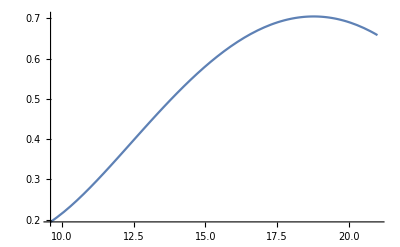

```mathematica
Plot[H1[a],{a,(96/10),21}]
```

```mathematica
H1'[a]//Simplify
H1''[a]//Simplify
```

-(ⅇ^(-a/12) (36012-27001 a+1000 a^2+12000 π^2))/(12000 π^2)

(ⅇ^(-a/12) (360024-51001 a+1000 a^2+12000 π^2))/(144000 π^2)

We can see the sign of the first derivative of H1[a] depends only on -(36012-27001 a+1000 a^2+12000 π^2), which is concave as a function of a. Thus, it suffices to check that 
Val3[a]:=12000 π^2 Exp[a/12]H1'[a], 
defined below, is positive at a=(96/10) and a=17.

```mathematica
Val3[a_]=-(36012-27001 a+1000 a^2+12000 π^2)//Simplify
```

-36012+27001 a-1000 a^2-12000 π^2

```mathematica
Val3[CenteredInterval[96/10,10^-2]]>0
Val3[CenteredInterval[17,10^-2]]>0
```

True

True

Using Pi<22/7  these can also be verified with rational arithmetic.

```mathematica
Val3[96/10]/.{Pi->22/7}
Val3[17]/.{Pi->22/7}
```

766053/61250

151649/9800

The sign of the second derivative depends only on (360024-51001 a+1000 a^2+12000 π^2), which is convex in a. Thus, to check it’s negative, we only need to check at a=17 and at a=21.

```mathematica
Val4[a_]=(360024-51001 a+1000 a^2+12000 π^2)//Simplify
Val4[CenteredInterval[17,10^-2]]<0
Val4[CenteredInterval[21,10^-2]]<0
```

360024-51001 a+1000 a^2+12000 π^2

True

True

Using Pi<22/7  these can also be checked with rational arithmetic.

```mathematica
Val4[17]/.{Pi->22/7}
Val4[21]/.{Pi->22/7}
```

-4873657/49

-7421853/49

Based on the above, it follows that H1 is either increasing or concave on all of [(96/10),21], and so has no local minima. Thus, we may check the positivity of H1 simply at the endpoints (96/10) and 21.

```mathematica
H1[CenteredInterval[96/10,10^-2]]>0

H1[CenteredInterval[21,10^-2]]>0
```

True

Hence, A<C.

#### B<C: See Eqn (156)

We have the partial of F w . r . t t2 @ (-1, 1), call it B and an upper bound B1. We will reuse our lower bound for C, C0, defined in the C<D subsection.

```mathematica
B1=f1[0,-1,1]f2[1,1,1]-f1[0,1,-1]f2[1,-1,-1]//Simplify
```

(3 a ⅇ^(-3 a/4) (1000-1500 a+1001 ⅇ^(a/2)))/(1000 π^2)

```mathematica
C0 2Pi^2Exp[a/4]/a//Simplify
B1 2Pi^2Exp[a/4]/a//Simplify
```

1/500 (-3001+1000 a) ⅇ^(-a/12)

3003/500+(6-9 a) ⅇ^(-a/2)

Factoring out Exp[-a/4]a/(2Pi^2), we must show the positivity of Val4 (defined below) on the interval [9.6,21]. Certainly Val4 is the sum of Val5 and Val6:

```mathematica
Val4[a_]=2Pi^2Exp[a/4]/a(C0-B1)//Simplify
Val5[a_]=(-3001/500+2 a) ⅇ^(-a/12);
Val6[a_]=-3003/500+(-6+9 a) ⅇ^(-a/2);
```

-3003/500+(-6+9 a) ⅇ^(-a/2)+(-3001/500+2 a) ⅇ^(-a/12)

Note that Val5[a] is concave for a <= 21, as immediately evident from the following derivative calculation:

```mathematica
Val5''[a]//Simplify
```

((-27001+1000 a) ⅇ^(-a/12))/72000

Now define

```mathematica
Val7[a_,b_]=-3003/500+(-6+9 a) ⅇ^(-b/2);
```

For a in [9.6,21] and any b>=a, Val7[a,b]<=Val6[a]. Moreover, for fixed b, Val7[a,b]+Val6[a] is concave in a. Thus, to show positivity of Val4[a] on [9.6,11], it suffices to show that the lower bound Val5[a]+Val7[a,11] is positive at a=9.6,11, which we check below. Similarly, to show positivity of Val4[a] on [11,21], it suffices to show that the lower bound Val5[a]+Val7[a,21] is positive at a=11,21. In fact, the positivity  of  Val5[a] + Val7[a, 11] at a = 11 is implied by the positivity of Val5[a]+Val7[a,21] at a=11 (so one of these checks is superfluous).

```mathematica
Val5[CenteredInterval[96/10,10^-2]]+Val7[CenteredInterval[96/10,10^-2],CenteredInterval[11,10^-2]]>0
Val5[CenteredInterval[11,10^-2]]+Val7[CenteredInterval[11,10^-2],CenteredInterval[11,10^-2]]>0
Val5[CenteredInterval[11,10^-2]]+Val7[CenteredInterval[11,10^-2],CenteredInterval[21,10^-2]]>0
Val5[CenteredInterval[21,10^-2]]+Val7[CenteredInterval[21,10^-2],CenteredInterval[21,10^-2]]>0
```

True

True

True

«1 more identical outputs»

Thus, B < C as required, completing the proof in the intermediate a case .

```mathematica
Clear[e,e2]
```

## 4 Points: Large A for Section D.3

again in this section, we set e = 1/1000, e2 = 1/100.

```mathematica
e=1/1000
e2=1/100
```

### (F-g)(-1,1/2)>=0, See equation (159) and surrounding text.

After algebraic simplifications in equation (159), the positivity of (F-g)(-1,1/2) is implied by the positivity of Val1:

```mathematica
Clear[a] 
Val1[a_]=FullSimplify[3Exp[-a/12]-2(1+e)^3+3a(2-4e)/(2Pi^2)]
```

Then since Val1 is convex in a, it suffices to check Val1 and Val1’ are positive at a=21:

```mathematica
Val1[CenteredInterval[21,10^-2]]>0
Val1'[CenteredInterval[21,10^-2]]>0
```

True

True

### Linearization portion for the region[-1, Cos[2 Pi Sqrt[3]/4] x[1/2, 1] (Proof of Lemma 21)

#### modules for interval arithmetic

The below function, minmakerx, takes in a set of functions of (x, u), a left endpoint, right endpoint, error radius, and a fixed u. Then with interval arithmetic, for each map in the set, it computes a lower bound for the map evaluated at the right and left endpoints, and sums intervals whose left endpoints are these lower bounds. Thus, it’s output is an interval whose left endpoint is a lower bound for the sum of the maps evaluated at either of the two endpoints. If every function in our set is monotone in x, as ours are, we obtain a rigorous lower bound for the sum of the functions on the entire interval [l,r].

```mathematica
Clear[minmakerx,minmakeru,segmentcheckerx,segmentcheckeru]
minmakerx[maps_,l_,r_,rad_,u_]:=Module[{int=Interval[{0-rad,0+rad}]},
For[j=1,j<=Length[maps], j++,
If[Min[Interval[maps[[j]][CenteredInterval[l,rad],u]]]<=Min[Interval[maps[[j]][CenteredInterval[r,rad],u]]],
int=int+Interval[maps[[j]][CenteredInterval[l,rad],u]];,
int=int+Interval[maps[[j]][CenteredInterval[r,rad],u]];
];
];
Return[int]
]
```

The next function segmentcheckerx, breaks an interval [a, b] into n equal length subintervals and applies minmakerx to each with a given set of functions . If segmentcheckerx returns true, we know that the sum of the functions is positive on the entire interval, so long as each function is monotone in x.

```mathematica
segmentcheckerx[maps_,a_,b_,n_,rad_,u_]:=Apply[And,
Table[minmakerx[maps,a+k*(b-a)/n,a+(k+1)*(b-a)/n,rad,u]>0,{k,0,n-1}]]
```

We have the analogous functions minmakeru and segmentcheckeru for checking segments where x is fixed and u varies .

```mathematica
minmakeru[maps_,l_,r_,rad_,x_]:=Module[{int=Interval[{0-rad,0+rad}]},
For[j=1,j<=Length[maps], j++,
If[Min[Interval[maps[[j]][x,CenteredInterval[l,rad]]]]<=Min[Interval[maps[[j]][x,CenteredInterval[r,rad]]]],
int=int+Interval[maps[[j]][x,CenteredInterval[l,rad]]];,
int=int+Interval[maps[[j]][x,CenteredInterval[r,rad]]];
];
];
Return[int]
]
segmentcheckeru[maps_,a_,b_,n_,rad_,x_]:=Apply[And,
Table[minmakeru[maps,a+k*(b-a)/n,a+(k+1)*(b-a)/n,rad,x]>0,{k,0,n-1}]]
```

#### Setup

Here is our lower bound for f, call it Flow . In the text, it's denoted \tilde{F} _T. We will use a different definition for Flow in the proof of the 6 point problem.

```mathematica
Flow[a_,x_,u_]:=(Exp[-a x^2]+Exp[-a(x-1)^2])Exp[-3a u^2]+Exp[-a(1/2-x)^2]Exp[-3a (1/2-u)^2]
```

When a=21, Flow[a_, x_, u_] decomposes as the sum of Val1, Val2, and Val3, each of which is clearly monotone in x and u for x, u in [0, 1/2] .

```mathematica
Val1[x_,u_]=Exp[-a x^2]Exp[-3a u^2]/.a->21;
Val2[x_,u_]=Exp[-a(x-1)^2]Exp[-3a u^2]/.a->21;
Val3[x_,u_]=Exp[-a(1/2-x)^2]Exp[-3a (1/2-u)^2]/.a->21;
Flow[21,x,u]-(Val1[x,u]+Val2[x,u]+Val3[x,u])//Simplify
```

0

We have the lower and upper bounds b1[-1], b1[1], respectively on the coefficient b1, obtained from equation 158:

```mathematica
b1[-1] =(2-4e) 3a Exp[-a/4]/(2Pi^2);
b1[1] = (1 + e)3 a Exp[-a/4]/(Pi^2);
```

It is straightforward to compute
g_ {c, d} = F (-1, 1) + b1 t2^2 + b1 (d t1 + c t2 - cd),
with which we obtain glinearbound[c, d, t1, t2] which is an upper bound  for g_ {c, d} when t1, c < 0, t2, d in [1/2, 1], as seen in equation 160. glinbound is the same function defined in terms of x' s and u' s instead of t1' s and t2' s (also times -1 because we want to think of adding this function to Flow to bound F-g below):

```mathematica
Clear[glinbound,glinbound2,glinearbound,x,u,a,t1,t2]
glinearbound[c_, d_,a_, t1_, t2_] := 2 (1 + e)^3 Exp[-a/4] + b1[-1] t2 (t2 +c) + b1[-1]*d *t1  - c*d *b1[1];
glinbound[c_, d_,a_][ x_, u_]:=-glinearbound[c,d,a,Cos[2Pi x],Cos[2Pi u]] ;
```

So we will use our segmentchecker functions to show that Flow-glinbound is positive on the segments indicated in equations 161-163 when a=21, since we have decomposed Flow into monotone functions in x and u, and glinbound is likewise monotone.

Similarly, we must show on those same segments that D[Exp[a/4]Flow-glinbound]/da is positive for a=21. Using Lemma 43, D[Exp[a/4]Flow]/da can be decomposed into the sum of Val_i for i=4,5,..,9 (see below), each of which is monotone in x and u. Moreover, it is proved in the text that D[Exp[a/4]glinbound]/da is also monotone in x and u.

```mathematica
Clear[term1,term2,term3,Val4,Val5,Val6,Val7,Val8,Val9,Dglinbound]
term1[x_,u_]:=x^2+3u^2-1/4
term2[x_,u_]:=(1/2-x)^2+3(1/2-u)^2-1/4
term3[x_,u_]:=(x-1)^2+3u^2-1/4
Val4[x_,u_]:=-(term1[x,u]-1/28)Exp[-21 term1[x,u]]
Val5[x_,u_]:=-1/28 Exp[-21term1[x,u]]
Val6[x_,u_]:=-(term2[x,u]-4/7)Exp[-21 term2[x,u]]
Val7[x_,u_]:=-4/7Exp[-21 term2[x,u]]
Val8[x_,u_]:=-(term3[x,u]-2/5)Exp[-21 term3[x,u]]
Val9[x_,u_]:=-2/5 Exp[-21 term3[x,u]]
(D[Flow[a,x,u]Exp[a/4],a]/.a->21)-(Val4[x,u]+Val5[x,u]+Val6[x,u]+Val7[x,u]+Val8[x,u]+Val9[x,u])//Simplify
Dglinbound[c_,d_,a_][x_,u_]=Simplify[D[Exp[a/4]glinbound[c,d,a][x,u],a]]//Simplify;
```

0

#### Verification

We first handle the 2 segments in equation 161, with a=21 for both Flow-glinbound and D[Exp[a/4]Flow-glinbound]/da:

```mathematica
a=21;
c=-1;
d=1;
xl=Sqrt[3]/4;
xr=1/2;
ul=ArcCos[1]/(2Pi);
ur=ArcCos[7/10]/(2Pi);
n=10;
rad=1/100000;
u=ArcCos[7/10]/(2Pi);
x=Sqrt[3]/4;
maps1={Val1,Val2,Val3,glinbound[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[x,rad]]
maps2={Dglinbound[c,d,a],Val4,Val5,Val6,Val7,Val8,Val9};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[x,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«1 more identical outputs»

```mathematica
Next, we handle the two segments in equations 162:
```

```mathematica
a=21;
c=-1;
d=7/10;
xl=Sqrt[3]/4;
xr=1/2;
ul=ArcCos[7/10]/(2Pi);
ur=ArcCos[6/10]/(2Pi);
n=10;
rad=1/100000;
u=ArcCos[6/10]/(2Pi);
x=Sqrt[3]/4;
maps1={Val1,Val2,Val3,glinbound[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[x,rad]]
maps2={Dglinbound[c,d,a],Val4,Val5,Val6,Val7,Val8,Val9};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[x,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«1 more identical outputs»

Finally, we handle the two segments from equation 163

```mathematica
a=21;
e=1/1000;
e2=1/100;
c=-1;
d=6/10;
xl=Sqrt[3]/4;
xr=1/2;
ul=ArcCos[6/10]/(2Pi);
ur=ArcCos[5/10]/(2Pi);
n=10;
rad=1/100000;
u=ArcCos[5/10]/(2Pi);
x=Sqrt[3]/4;
maps1={Val1,Val2,Val3,glinbound[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[x,rad]]
maps2={Dglinbound[c,d,a],Val4,Val5,Val6,Val7,Val8,Val9};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[x,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«1 more identical outputs»

This final check completes the proof of Lemma 21

### d(F-G)/dt_1, d^2(F-G)/dt_1dt_2>=0 at p* (Proof of Lemma 22)

First, we handle the first derivative inequality. Set x=sqrt(3)/4, u=sqrt(3)/12. 
To obtain the bound in equation 166, we need to prove the 4 inequalities claimed right after that line for all a>=21:
x-(1-x)Exp[-a(1-2x)]>=39/100
(1/2-x)2(1+e)Exp[-a(1-x-3u)]<=1/100
sin(2pi x)<=41/100
cos(2pi u)<=62/100
The 3rd and 4th inequalities are straightforward checks, and for the first two, we simply use monotonicity in the variable a to reduce our check to the case when a=21

```mathematica
Val1[x_,u_,a_]=x-(1-x)Exp[-a(1-2x)];
Val2[x_,u_,a_]=(1/2-x)2(1+e)Exp[-a(1-x-3u)];
Val1[CenteredInterval[Sqrt[3]/4, 10^-3],CenteredInterval[Sqrt[3]/12, 10^-3],CenteredInterval[21, 10^-2]]>39/100
Val2[CenteredInterval[Sqrt[3]/4, 10^-3],CenteredInterval[Sqrt[3]/12, 10^-3],CenteredInterval[21, 10^-2]]<1/100
Sin[2Pi CenteredInterval[Sqrt[3]/4,10^-4]]<41/100
Cos[2Pi CenteredInterval[Sqrt[3]/12,10^-4]]<62/100
```

True

True

True

«1 more identical outputs»

```mathematica
x=Sqrt[3]/4;
u=Sqrt[3]/12;
Val1[x_,u_,a_]x-(1-x)Exp[-a(1-2x)]
N[(1/2-x)2(1+e)Exp[-a(1-x-3u)]/.{a->21,e->1000}]
N[Sin[2Pi x]]
N[Cos[2Pi u]]
Clear[x,u]
```

0.398995

8.04607

0.408576

0.616191

All that' s left is to check the final inequality in equation 169, which is straightforward by bounding Pi above by 22/7:

```mathematica
Val3=38/41-3(1+e)62/(100Pi)
(Val3/.{Pi->22/7})>0
```

38/41-93093/(50000 π)

True

Now onto the mixed partial inequality.
We again have two simple inequalities to verify after equation 173:
u-(1-u)Exp[-3a(1-2u)]>=14/100
Sin[2Pi u]<= 4/5
The second inequality is straightforward and the first quantity is monotone in a, so suffices to check at a=21 to ensure it holds for all a>=21.

```mathematica
Val4[u_,a_]=u-(1-u)Exp[-3a(1-2u)];
Val4[CenteredInterval[Sqrt[3]/12, 10^-3],CenteredInterval[21, 10^-2]]>14/100
Sin[2Pi CenteredInterval[Sqrt[3]/12, 10^-3]]<4/5
```

True

True

Now all that remains is to check the positivity of the final quantity in equation 175. It’s rational so no need for interval arithmetic:

```mathematica
Val5[a_]=14*5*3*39*a/(100*4*41)-3(1+e);
Val5[21]>0
```

True

This calculation completes the proof of Lemma 22 and the 4 point case for a>=21.

```mathematica
Clear[e,e2]
```

## 6 Points: Large A for Section D.4

We again use e = 1/1000, e2 = 1/100

```mathematica
e=1/1000;
e2=1/100;
```

### Coefficient Bounds in Section D.4.1

-1 as an argument will yield lower bounds, 1 for upper bound. Run this section to get all the bounds

These computations give the a01 bounds

```mathematica
a01[-1]=f1[0,1,-1]f2[1,-1/2,-1];
a01[1]=f1[0,1,1]f2[1,-1/2,1];
```

These computations give the a10 bounds

```mathematica
b=-1;
(f1[0,1,b]f2[0,-1/2,b]-f1[0,-1,-b]f2[0,1/2,-b])/2+a01[b]/2
b=1;
(f1[0,1,b]f2[0,-1/2,b]-f1[0,-1,-b]f2[0,1/2,-b])/2+a01[b]/2
Clear[b]
```

-(502001 ⅇ^(-a/3))/1000000+(333 √3 a ⅇ^(-a/3))/(1000 π)

-(997999 ⅇ^(-a/3))/2000000+(1001 a ⅇ^(-a/3))/(1000 √3 π)

Since (1 + e)^2 < 1 + 3 e, we obtain

```mathematica
a10[-1]=(-1-6e) ⅇ^(-a/3)/2+(a (1-e) ⅇ^(-a/3))/(√3 π);
a10[1]=(-1+3e) ⅇ^(-a/3)/2+(a (1+e) ⅇ^(-a/3))/(√3 π);
```

The next computations produce the bounds for a00, again using the fact that (1 + e)^2 < 1 + 3 e.

```mathematica
b=-1;
a00[-1]=(f1[0,1,b]f2[0,-1/2,b]+f1[0,-1,b]f2[0,1/2,b])/2
b=1;
(f1[0,1,b]f2[0,-1/2,b]+f1[0,-1,b]f2[0,1/2,b])/2
a00[1]=3/2 (1+3e) ⅇ^(-a/3)
```

(3 ⅇ^(-a/3))/2

(3006003 ⅇ^(-a/3))/2000000

(3009 ⅇ^(-a/3))/2000

Next, we compute a02 bound with the formula a02 = 4/9 f1 (-1) (f2 (-1) - f2 (1/2) + 3/2 f2' (1/2)) . For the lower bound, we throw away the f2 (-1), for the upper bound, we bound f1 (-1) f2 (-1) by Exp[-a/3] *e2 (corresponding to epsilon_2 in the text) .

```mathematica
a02[-1]=4/9f1[0,-1,-1](-f2[0,1/2,1]+3/2f2[1,1/2,-1])
a02[1]=4/9f1[0,-1,1](-f2[0,1/2,-1]+3/2f2[1,1/2,1])+e2 Exp[-a/3]
```

8/9 ⅇ^(-a/4) (-(1001 ⅇ^(-a/12))/1000+(999 √3 a ⅇ^(-a/12))/(2000 π))

ⅇ^(-a/3)/100+(1001 ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))/1125

Finally, we compute the b00 bound by using the formula 
b00 = a00 + a02/4

```mathematica
b00[-1]=a02[-1]/4+a00[-1]
b00[1]=a02[1]/4+a00[1]
```

(3 ⅇ^(-a/3))/2+2/9 ⅇ^(-a/4) (-(1001 ⅇ^(-a/12))/1000+(999 √3 a ⅇ^(-a/12))/(2000 π))

(3009 ⅇ^(-a/3))/2000+1/4 (ⅇ^(-a/3)/100+(1001 ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))/1125)

```mathematica
a00[-1]Exp[a/3]
a00[1]Exp[a/3]
a01[-1]Exp[a/3]
a01[1]Exp[a/3]
a10[-1]Exp[a/3]
a10[1]Exp[a/3]
a02[-1]Exp[a/3]
a02[1]Exp[a/3]
b00[-1]Exp[a/3]
b00[1]Exp[a/3]
```

3/2

3009/2000

(333 √3 a)/(500 π)

(1001 a)/(500 √3 π)

ⅇ^(a/3) (-(503 ⅇ^(-a/3))/1000+(333 √3 a ⅇ^(-a/3))/(1000 π))

ⅇ^(a/3) (-(997 ⅇ^(-a/3))/2000+(1001 a ⅇ^(-a/3))/(1000 √3 π))

8/9 ⅇ^(a/12) (-(1001 ⅇ^(-a/12))/1000+(999 √3 a ⅇ^(-a/12))/(2000 π))

ⅇ^(a/3) (ⅇ^(-a/3)/100+(1001 ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))/1125)

ⅇ^(a/3) ((3 ⅇ^(-a/3))/2+2/9 ⅇ^(-a/4) (-(1001 ⅇ^(-a/12))/1000+(999 √3 a ⅇ^(-a/12))/(2000 π)))

ⅇ^(a/3) ((3009 ⅇ^(-a/3))/2000+1/4 (ⅇ^(-a/3)/100+(1001 ⅇ^(-a/4) (-ⅇ^(-a/12)+(√3 a ⅇ^(-a/12))/(2 π)))/1125))

### Necessary Derivative Conditions in Section D.4.2

#### t1 derivative at (-1,1) (Equation 181)

it suffices to show the t1 deriv of g at (-1, 1) is negative, we call this quantity Val1, up to a factor of Exp[a/3]. Val1 is linear in a. So we show it’s negative at a=(96/10), and clearly it’s coefficient of a is negative.

```mathematica
Val1[a_]=Exp[a/3](a10[1]-a02[-1])//Simplify
Val1[CenteredInterval[96/10,10^-2]]<0
```

(-1986 √3 a+7043 π)/(18000 π)

True

#### t1 derivative at (-1, 1/2) (Equations 182, 184-186)

We must bound below f1' (-1) f2 (1/2) - a10 - a02/2, and we call our lower bound Val2, up to a factor of Exp[a/3]. We want to show Val2 is positive for all a>=9.6. Similar to the previous case, the factor of Exp[a/3] makes Val2 quadratic in a, so we just check  positivity of the coefficient of a^2, value and derivative at a=(96/10)

```mathematica
Val2[a_]=Exp[a/3](f1[1,-1,-1]f2[0,1/2,-1]-a10[1]-a02[1]/2)//Simplify
Val2[CenteredInterval[96/10,10^-2]]>0
Val2'[CenteredInterval[96/10,10^-2]]>0
Val2''[a]
```

(9000 a^2+16891 π^2-10 a (1800+1001 √3 π))/(18000 π^2)

True

True

1/π^2

#### t1 derivative at (1, -1/2) (Equation 183, 187-189)

We must bound above f1' (1) f2 (-1/2) - a10 + a02/2, and we call our upper bound Val3 up to a factor of Exp[a/3]. The factor of Exp[a/3] makes Val3 linear in a, and it is positive for a=0. So we just need check Val3 is negative at a = 96/10 to show it is negative for all a>=9.6.

```mathematica
Clear[Val3]
Val3[a_]=Exp[a/3](f1[1,1,1]f2[0,-1/2,1]-a10[-1]+a02[1]/2)//FullSimplify
Val3[CenteredInterval[96/10,10^-2]]<0
```

(9009 a-1990 √3 a π+1136 π^2)/(18000 π^2)

True

### Linearization Portion of the proof in Section D.4.3

#### modules for interval arithmetic (same as in 4-point linearization proof)

The below function, minmakerx, takes in a set of functions of (x, u), a left endpoint, right endpoint, error radius, and a fixed u. Then with interval arithmetic, for each map in the set, it computes a lower bound for the map evaluated at the right and left endpoints, and sums intervals whose left endpoints are these lower bounds. Thus, it’s output is an interval whose left endpoint is a lower bound for the sum of the maps evaluated at either of the two endpoints. If every function in our set is monotone in x, as ours are, we obtain a rigorous lower bound for the sum of the functions on the entire interval [l,r].

```mathematica
Clear[minmakerx,minmakeru,segmentcheckerx,segmentcheckeru]
minmakerx[maps_,l_,r_,rad_,u_]:=Module[{int=Interval[{0-rad,0+rad}]},
For[j=1,j<=Length[maps], j++,
If[Min[Interval[maps[[j]][CenteredInterval[l,rad],u]]]<=Min[Interval[maps[[j]][CenteredInterval[r,rad],u]]],
int=int+Interval[maps[[j]][CenteredInterval[l,rad],u]];,
int=int+Interval[maps[[j]][CenteredInterval[r,rad],u]];
];
];
Return[int]
]
```

The next function segmentcheckerx, breaks an interval [a, b] into n equal length subintervals and applies minmakerx to each with a given set of functions . If segmentcheckerx returns true, we know that the sum of the functions is positive on the entire interval, so long as each function is monotone in x.

```mathematica
segmentcheckerx[maps_,a_,b_,n_,rad_,u_]:=Apply[And,
Table[minmakerx[maps,a+k*(b-a)/n,a+(k+1)*(b-a)/n,rad,u]>0,{k,0,n-1}]]
```

We have the analogous functions minmakeru and segmentcheckeru for checking segments where x is fixed and u varies .

```mathematica
minmakeru[maps_,l_,r_,rad_,x_]:=Module[{int=Interval[{0-rad,0+rad}]},
For[j=1,j<=Length[maps], j++,
If[Min[Interval[maps[[j]][x,CenteredInterval[l,rad]]]]<=Min[Interval[maps[[j]][x,CenteredInterval[r,rad]]]],
int=int+Interval[maps[[j]][x,CenteredInterval[l,rad]]];,
int=int+Interval[maps[[j]][x,CenteredInterval[r,rad]]];
];
];
Return[int]
]
segmentcheckeru[maps_,a_,b_,n_,rad_,x_]:=Apply[And,
Table[minmakeru[maps,a+k*(b-a)/n,a+(k+1)*(b-a)/n,rad,x]>0,{k,0,n-1}]]
```

#### Setup

We define Flow ( in the text as \tilde{F}_T) as in equation 76

```mathematica
Clear[a,x,u,Flow,glinearbound,glinbound]
Flow[a_,x_,u_]:=(Exp[-a x^2]+Exp[-a(x-1)^2])Exp[-3a u^2]
```

When a = 96/10, Flow decomposes as the sum of Val1 and Val2, each of which is monotone in x and u, thus compatible with our segmentchecker functions

```mathematica
Clear[Val1,Val2]
Val1[x_,u_]=Exp[-a x^2]Exp[-3a u^2]/.{a->96/10};
Val2[x_,u_]=Exp[-a(x-1)^2]Exp[-3a u^2]/.{a->96/10};
```

Depending on the choice of c and d, we need different upper bounds for g, as indicated in equations 190 and 191. glinbound corresponds to equation 190 and glinbound2 corresponds to equation 191.

```mathematica
Clear[glinearbound,glinbound,glinearbound2,glinbound2]
glinearbound[c_,d_,a_,t1_,t2_]:=b00[1]+a10[-1]t1+ a01[1]t2+a02[1]t2^2+a02[-1](d t1 +c t2- c d)
glinbound[c_,d_,a_][x_,u_]:=-glinearbound[c,d,a,Cos[2Pi x],Cos[2Pi u]];
glinearbound2[c_,d_,a_,t1_,t2_]:=b00[1]+a10[-1]t1+ a01[-1]t2+a02[1]t2^2+a02[1](d t1 +c t2- c d);
glinbound2[c_,d_,a_][x_,u_]:=-glinearbound2[c,d,a,Cos[2Pi x],Cos[2Pi u]];
```

So we will use our segmentchecker functions to show that Flow - glinbound is positive on the 10 segments indicated after equation 191 when a = 21, since we have decomposed Flow into monotone functions in x and u, and glinbound, glinbound2 are similarly monotone in x and convex in t2, thus it suffices to check for maxima at endpoints of intervals).

Similarly, we must show on those same segments that D[Exp[a/3] Flow - glinbound/glinbound2]/da is positive for a = 96/10. Using the reasoning of Lemma 43, D[Exp[a/3] Flow]/da can be decomposed into the sum of Val_i for i = 3, 4,5,6 (see below), each of which is monotone in x and u . Moreover, it is clear that D[Exp[a/3] glinbound]/da is also monotone in x and u .

```mathematica
Clear[term1,term2,term3,Val3,Val4,Val5,Val6,Val7,Val8,Val9,x,u]
term1[x_,u_]:=x^2+3u^2-1/3;
term2[x_,u_]:=(x-1)^2+3u^2-1/3;
Val3[x_,u_]=-(term1[x,u]-9/16)Exp[-96/10term1[x,u]];
Val4[x_,u_]=-9/16Exp[-96/10term1[x,u]];
Val5[x_,u_]=-(term2[x,u]-9/16)Exp[-96/10term2[x,u]];
Val6[x_,u_]=-9/16Exp[-96/10term2[x,u]];
(D[Flow[a,x,u]Exp[a/3],a]/.a->96/10)-(Val3[x,u]+Val4[x,u]+Val5[x,u]+Val6[x,u])//Simplify
Dglinbound[c_,d_,a_][x_,u_]=Simplify[D[Exp[a/3]glinbound[c,d,a][x,u],a]]//Simplify;
Dglinbound2[c_,d_,a_][x_,u_]=Simplify[D[Exp[a/3]glinbound2[c,d,a][x,u],a]]//Simplify;
```

0

#### Verification

First, we consider the segments {(-Sqrt[2]/2, t2) for t2 in [1/4, 1/2]} and {(t1, 1/4), for t1 in [-1,-Sqrt[2]/2]}  when a=96/10 (see the first item in the list of segments below equation 191).

```mathematica
a=96/10;
c=-1;
d=1/2;
xl=1/2;
xr=3/8;
ul=ArcCos[1/4]/(2Pi);
ur=ArcCos[1/2]/(2Pi);
n=70;
rad=1/100000;
u=ArcCos[1/4]/(2Pi);
x=3/8;
maps1={Val1,Val2,glinbound[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[x,rad]]
maps2={Val3,Val4,Val5,Val6,Dglinbound[c,d,a]};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[x,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«1 more identical outputs»

Next, we consider the segments from the second item on the list : {(-Sqrt[2]/2, t2) for t2 in[0, 1/4]} and {(t1, 0), for t1 in[-1, -Sqrt[2]/2]}

```mathematica
a=96/10;
e=1/1000;
e2=1/100;
c=-1;
d=1/4;
xl=1/2;
xr=3/8;
ul=ArcCos[1/4]/(2Pi);
ur=ArcCos[0]/(2Pi);
n=30;
rad=1/100000;
u=ArcCos[0]/(2Pi);
x=3/8;
maps1={Val1,Val2,glinbound[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[x,rad]]
maps2={Val3,Val4,Val5,Val6,Dglinbound[c,d,a]};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[x,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«1 more identical outputs»

This check completes the proof of Lemma 33.

We now consider the third group of segments, now using glinbound2 as our upper bound for g. These segments are:
{(-sqrt[2]/2, t2) for t2 in [-1/10, 0]}, {(0, t2) for t2 in [-1/10, 0]} and {(t1, -1/10), for t1 in [ -Sqrt[2]/2,0]}

```mathematica
a=96/10;
c=-Sqrt[2]/2;
d=0;
xl=ArcCos[0]/(2Pi);
xr=3/8;
ul=ArcCos[-1/10]/(2Pi);
ur=ArcCos[0]/(2Pi);
n=30;
rad=1/100000;
u=ArcCos[-1/10]/(2Pi);
x=3/8;
maps1={Val1,Val2,glinbound2[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[xl,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[xr,rad]]
maps2={Val3,Val4,Val5,Val6,Dglinbound2[c,d,a]};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[xl,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[xr,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«3 more identical outputs»

Finally, we consider the segments {(-sqrt[2]/2, t2) for t2 in[-1/5, -1/10]}, {(0, t2) for t2 in[-1/5, -1/10]} and {(t1, -1/5), for t1 in[-Sqrt[2]/2, 0]}

```mathematica
a=96/10;
c=-Sqrt[2]/2;
d=-1/10;
xl=ArcCos[0]/(2Pi);
xr=3/8;
ul=ArcCos[-1/10]/(2Pi);
ur=ArcCos[-1/5]/(2Pi);
n=30;
rad=1/100000;
u=ArcCos[-1/5]/(2Pi);
x=3/8;
maps1={Val1,Val2,glinbound2[c,d,a]};
segmentcheckerx[maps1,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[xl,rad]]
segmentcheckeru[maps1,ul,ur,n,rad,CenteredInterval[xr,rad]]
maps2={Val3,Val4,Val5,Val6,Dglinbound2[c,d,a]};
segmentcheckerx[maps2,xl,xr,n,rad,CenteredInterval[u,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[xl,rad]]
segmentcheckeru[maps2,ul,ur,n,rad,CenteredInterval[xr,rad]]
Clear[c,d,xl,xr,ul,ur,n,rad,u,x,maps1,a,maps2]
```

True

True

True

«3 more identical outputs»

This final check completes the proof of Lemma 36.

### t1 derivative of the difference at (-Sqrt[2]/2,0) in D.4.4

We have a lower bound for the t1 deriv of F at (-Sqrt[2]/2, 0), meanwhile the t1 deriv of g at (-Sqrt[2]/2, 0) is a10. Thus, a lower bound for the difference, up to a factor of Exp[a/3], is given by Val1[a] as in Equation 194:

```mathematica
Val1[a_]=Sqrt[2]a Exp[a/192](3-5Exp[-a/4])/(8Pi)-(Exp[a/3]a10[1]//Simplify)
```

(a ⅇ^(a/192) (3-5 ⅇ^(-a/4)))/(4 √2 π)-(2002 √3 a-2991 π)/(6000 π)

As in the text, we claim Val1 is positive for a = 96/10 and increasing for a >= 96/10. The first of these is checked below,.

```mathematica
Val1[CenteredInterval[96/10,10^-2]]>0
```

True

The derivative computation in equation 196 is verified below  by decomposing Val1 into Val2 +Val3:

```mathematica
Val2[a_]=Sqrt[2]a Exp[a/192](3-5Exp[-a/4])/(8Pi);
Val3[a_]=-(Exp[a/3]a10[1]//Simplify);
```

```mathematica
Val2'[a]//Simplify
Val3'[a]//Simplify
```

(ⅇ^(-47 a/192) (-960+235 a+576 ⅇ^(a/4)+3 a ⅇ^(a/4)))/(768 √2 π)

-1001/(1000 √3 π)

We discard the positive quantity -960+235a to obtain Val4 (see equation 197) as a lower bound for Val2’[a]. Val4 is clearly increasing in a (see below), and Val3’[a] is constant in a, so it remains to check Val4[a]+Val3’[a]>0 for a=9.6, also handled below

```mathematica
Val4[a_]=(ⅇ^(-47 a/192) (576 ⅇ^(a/4)+3 a ⅇ^(a/4)))/(768 √2 π)//Simplify
Val4[CenteredInterval[96/10,10^-2]]+Val3'[a]>0
```

((192+a) ⅇ^(a/192))/(256 √2 π)

True

Hence Lemma 34 holds

### Positivity of L1 in D.4.5

We first prove the bounds on f1 (-1) f2 (1/2)-f1(1)f2(-1/2) between equations 204 and 205.

```mathematica
b=-1;
f1[0,-1,b]f2[0,1/2,b]-f1[0,1,-b]f2[0,-1/2,-b]//Simplify
b=1;
f1[0,-1,b]f2[0,1/2,b]-f1[0,1,-b]f2[0,-1/2,-b]//Simplify
Clear[b]
```

-((-1+2 e+e^2) ⅇ^(-a/3))

(1+4 e+2 e^2) ⅇ^(-a/3)

This along with the fact that e^2 < e yields the first inequalities on (1-3epsilon)Exp[-a/3]<=f1 (-1) f2 (1/2) - f1 (1) f2 (-1/2) <=(1+6e)Exp[-a/3] (we also already did this in computing bounds on a10).

Next we check that a10[-1] - a02[1]/2 is positive as referenced after equation 207.

```mathematica
Val1[a_]=a10[-1]-a02[1]/2 //Simplify
Val1[CenteredInterval[96/10,10^-2]]>0
```

(ⅇ^(-a/3) (995 √3 a-568 π))/(9000 π)

True

Now when t1 = 1, we have an upper bound on (f1(-1) f2 (1/2) - f1 (1) f2 (-1/2)+a02)/(a10+a02 t2)
given after equation 207, the final term of which, call it Val2, we claim is decreasing in a. Indeed that is easy to see just by taking the derivative with respect to a, whose numerator is maximized when t2=-1/2 but still remains negative as seen below:

```mathematica
Val2[a_]=(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1]))//Simplify
Val2'[a]//Simplify
Val2'[a]/.{t2->-1/2}//Simplify
```

-(4 (1001 √3 a+284 π))/(-√3 a (2997+4004 t2)+π (4527+7918 t2))

-(36 √3 π (598075+1007006 t2))/(√3 a (2997+4004 t2)-π (4527+7918 t2))^2

-(3404592 √3 π)/(995 √3 a-568 π)^2

In sum then, for some a>=9.6, L1(1, t2) >= 0 when t2 in [-1/2, 0] if the following lower bound, Val3, is positive for a=(96/10)

```mathematica
Val3[u_,a_]=3u(1-e)2Pi/((1+e)Sin[2Pi u])-2-(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1]))//Simplify
Val3[u_,96/10]
```

(-2 √3 a (4999+4004 t2)+7918 (π+2 π t2))/(√3 a (2997+4004 t2)-π (4527+7918 t2))+(5994 π u Csc[2 π u])/1001

(-96/5 √3 (4999+4004 t2)+7918 (π+2 π t2))/(48/5 √3 (2997+4004 t2)-π (4527+7918 t2))+(5994 π Csc[2 π u_] u_)/1001

Val3[u_, 96/10] is the difference of Val4 and Val5, defined below, each of which is increasing in u (see Lemma 45 and recall t2=Cos[2Piu]). Thus, we can show their difference is positive on the interval [1/4,1/3] which the segment check module.

```mathematica
Val4[u_]=3u(1-e)2Pi/((1+e)Sin[2Pi u])//Simplify
Val5[u_]=2+(1+6e+Exp[a/3]a02[1])/(Exp[a/3](a10[-1]+t2 a02[1]))/.{a->96/10,t2->Cos[2Pi u]}//Simplify
```

(5994 π u Csc[2 π u])/1001

(479904 √3-39590 π+4 (96096 √3-19795 π) Cos[2 π u])/(9 (15984 √3-2515 π)+2 (96096 √3-19795 π) Cos[2 π u])

The following plot is just to give a picture for these two increasing functions in u :

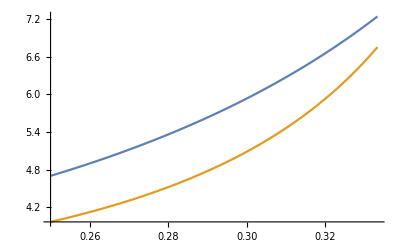

```mathematica
Plot[{Val4[u],Val5[u]},{u,1/4,1/3}]
```

We next use the SegmentCheck function to verify that Val4>Val5 dividing into 14 subintervals (13 is too small for this case).

```mathematica
SegmentCheck[Val4,Val5,{1/4,1/3,14}]
```

True

This completes the t1=1 case of showing L1 is positive. Now when t1 = 0, we arrive at needing to show the positivity of Equation 209 when a=9.6. Call the two terms in that equation Val6 and Val7.

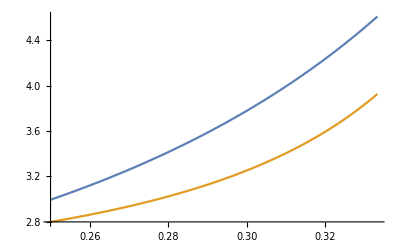

```mathematica
Val6[u_]=12u(1-e)/((1+e)Sin[2Pi u])//Simplify;
Val7[u_]=2+(1+6e)/(Exp[a/3](a10[-1]+t2 a02[1]))/.{a->96/10, t2->Cos[2Pi u]}//Simplify;
Plot[{Val6[u],Val7[u]},{u,1/4,1/3}]
```

In the text, they are proved to be increasing in u . So we again may use segment check to show their difference is positive.    We again use the SegmentCheck function to verify that Val6>Val7 dividing into 10 subintervals (9 is too small for this case).

```mathematica
SegmentCheck[Val6,Val7,{1/4,1/3,10}]
```

False

### Negativity of N in D.4.6

As referenced in the appendix, it remains to show the following quantity, Val1[a] is negative for a >= (96/10)a. As it' s quadratic in a, we make the usual checks of value and first two derivatives at a=(96/10) to ensure this holds.

```mathematica
Val1[a_]=Exp[2a/3](a02[1](a00[1]+a10[1])-a01[-1]a10[-1])//Simplify
Val1[CenteredInterval[96/10,10^-2]]<0
Val1'[CenteredInterval[96/10,10^-2]]<0
Val1''[a]
```

-(2970003 a^2-6601550 √3 a π+11948262 π^2)/(13500000 π^2)

True

True

-990001/(2250000 π^2)

### Positivity of L2 in D.4.6

Our first check for this portion is the positivity of the final lower bound in equation 212, call it Val1 (up to a factor of Pi). Since it is quadratic in a, we make the usual check of positive value, first and second derivative for a=96/10 to get positivity for all a>=96/10.

```mathematica
Val1[a_]=Pi ⅇ^(a/3) (a10[-1]+a02[1] t2)-1/4 a ⅇ^(a/3) (b00[1]+a01[-1] t2+a02[1] t2^2)/.{t2->-1/5}//Simplify
Val1[CenteredInterval[96/10,10^-2]]>0
Val1'[CenteredInterval[96/10,10^-2]]>0
Val1''[a]
```

(941 √3 a^2+(-281107+219620 √3) a π-294340 π^2)/(900000 π)

True

True

941/(150000 √3 π)

That completes the proof that L2 >0 at (0. - .2). Now we are onto the case of showing L2(-Sqrt[2]/2, 0)>0.
We have to show that the quantity preceding Equation 218 is positive, and we decompose it into the sum of Val2, Val3, and Val4:

We have to show that 4Pi Sqrt[2]/a (1+Exp[-a/4])/(3-(5-e)Exp[-a/4])+Sqrt[2]/2-b00[1]/a10[-1]>=0

```mathematica
Val2[a_]=4Pi Sqrt[2]Exp[a/3] a10[-1](1+Exp[-a/4])/(3-(5-e)Exp[-a/4]);
Val3[a_]=Sqrt[2]/2(a)(Exp[a/3] a10[-1]);
Val4[a_]=-a Exp[a/3]b00[1];
```

Now for 9.6 <= a <= c, we have a lower bound on Val2[a] given by Val5[a,c] (see equation 218):

```mathematica
Clear[Val5]
Val5[a_]=4Pi Sqrt[2]Exp[a/3] a10[-1](1+Exp[-c/4])/(3-(5-e)Exp[-c/4]);
```

Then L3, as defined in the text, is simply the sum of Val3, Val4, and Val5 . By finding for each a >=9.6 a corresponding c>=a such that L3(a,c)>0, we would prove L2(-Sqrt[2]/2,0)>0 as desired. 
To do so, we take the sequence a_0,...,a_6:=9.6,9.8,10,10.2,11,12,infinity, we check that if a is in [a_i,a_{i+1}], then L(a,a_{i +1})>0. Each of these checks is simple since L3(a,c) is quadratic and convex up (shown below) in a for fixed c, and so we can verify that for a>=a_i, L3(a,a_{i+1}) is positive and increasing by checking L3(a_i,a_{i+1})>0 and L3’(a_i,a_{i+1})>0 where “prime” refers to derivative with respect to the first argument.  These checks are handled with the following for loop:

```mathematica
L3[a_]=Val3[a]+Val4[a]+Val5[a];
L3''[a]//Simplify
Module[{list1={9.6,9.8,10,10.2,11,12}},
For[i=1,i<Length[list1],i++,
l=list1[[i]];
r=list1[[i+1]];
Print[l," ",r," ",
(L3[CenteredInterval[l,10^-4]]/.{c->CenteredInterval[r,10^-2]})>0,
" ",
(L3'[CenteredInterval[l,10^-4]]/.{c->CenteredInterval[r,10^-2]})>0]
]
]
```

(-2002+2997 √2)/(3000 √3 π)

9.6 9.8 True True

9.8 10 True True

10 10.2 True True

10.2 11 True True

11 12 True True

It only remains to consider the case where c=infinity, where we use the fact that for all real-valued c, Val5[a,c]>=4Pi Sqrt[2]Exp[a/3] a10[-1](1/3), which Mathematica obtains by plugging in c=Infinity:

```mathematica
Val5[a]
Val5[a]/.c->Infinity
```

(4 √2 ⅇ^(a/3) (1+ⅇ^(-c/4)) (-(503 ⅇ^(-a/3))/1000+(333 √3 a ⅇ^(-a/3))/(1000 π)) π)/(3-(4999 ⅇ^(-c/4))/1000)

4/3 √2 ⅇ^(a/3) (-(503 ⅇ^(-a/3))/1000+(333 √3 a ⅇ^(-a/3))/(1000 π)) π

With that bound, we make our final check of L3 :

```mathematica
(L3[CenteredInterval[12,10^-3]]/.{c->Infinity})>0
(L3'[CenteredInterval[12,10^-3]]/.{c->Infinity})>0
```

True

True